## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = True;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_GAPD";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.408 | 0.3876
0.4284 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.0008455
0.0009345 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0.7,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.408 | 0.3876
0.4284 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
0.7 | g3p | 0.00089 | 0.0008455
0.0009345 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 | M | 8.9 | 22 | teoa | 0.04 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,Overscript[(GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c, GAPD2],((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,Overscript[(GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c, GAPD4],((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};
```

### Simulate data without uncertainty

```mathematica
Export["GAPDSimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["GAPDSimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\haldaneRatio_1.txt"	0.408
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"C:\MASSef\examples\fit_GAPD\input\absRateFor.txt"	268
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7	25	"C:\MASSef\examples\fit_GAPD\input\customRatio_1.txt"	425.

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.991661188858
best_fit: 0.934616132575
best_fit: 1.01568528154
best_fit: 2.80388671398
best_fit: 0.968821864108

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat⟦2⟧ is longer than depth of object.

```mathematica
lmaResultsFileNew
```

/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/output/raw/lmaResults_GAPD_20175241235.txt

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | haldaneRatio_1 | 0.000204157 | 4.16799×10^-8 | 0.0470198 | 0.408 | 0.408192
1 | relRateFor_nad | 0.00198267 | 3.93099×10^-6 | 0.455487 | 0.0909091 | 0.090495
1 | relRateFor_nad | 0.00188279 | 3.54489×10^-6 | 0.43259 | 0.136807 | 0.136215
1 | relRateFor_nad | 0.00174357 | 3.04005×10^-6 | 0.400668 | 0.20076 | 0.199956
1 | relRateFor_nad | 0.00156068 | 2.43573×10^-6 | 0.358715 | 0.284747 | 0.283726
1 | relRateFor_nad | 0.00133821 | 1.7908×10^-6 | 0.307659 | 0.386863 | 0.385673
1 | relRateFor_nad | 0.00109159 | 1.19157×10^-6 | 0.251032 | 0.5 | 0.498745
1 | relRateFor_nad | 0.000844832 | 7.13741×10^-7 | 0.194341 | 0.613137 | 0.611945
1 | relRateFor_nad | 0.000621991 | 3.86872×10^-7 | 0.143116 | 0.715253 | 0.714229
1 | relRateFor_nad | 0.000438625 | 1.92392×10^-7 | 0.100946 | 0.79924 | 0.798433
1 | relRateFor_nad | 0.000298947 | 8.93691×10^-8 | 0.0688113 | 0.863193 | 0.862599
1 | relRateFor_nad | 0.000198675 | 3.94718×10^-8 | 0.0457361 | 0.909091 | 0.908675
0.7 | relRateFor_g3p | 0.00512405 | 0.0000262559 | 1.17292 | 0.0909091 | 0.0898428
0.7 | relRateFor_g3p | 0.0048668 | 0.0000236857 | 1.11437 | 0.136807 | 0.135282
0.7 | relRateFor_g3p | 0.00450808 | 0.0000203228 | 1.03266 | 0.20076 | 0.198687
0.7 | relRateFor_g3p | 0.00403655 | 0.0000162937 | 0.925144 | 0.284747 | 0.282113
0.7 | relRateFor_g3p | 0.00346255 | 0.0000119892 | 0.794111 | 0.386863 | 0.383791
0.7 | relRateFor_g3p | 0.00282571 | 7.98462×10^-6 | 0.648531 | 0.5 | 0.496757
0.7 | relRateFor_g3p | 0.00218793 | 4.78705×10^-6 | 0.502523 | 0.613137 | 0.610056
0.7 | relRateFor_g3p | 0.00161148 | 2.59686×10^-6 | 0.370369 | 0.715253 | 0.712604
0.7 | relRateFor_g3p | 0.00113679 | 1.29229×10^-6 | 0.261413 | 0.79924 | 0.797151
0.7 | relRateFor_g3p | 0.000774981 | 6.00596×10^-7 | 0.178287 | 0.863193 | 0.861654
0.7 | relRateFor_g3p | 0.000515134 | 2.65363×10^-7 | 0.118544 | 0.909091 | 0.908013
1 | relRateFor_pi | 0.000294558 | 8.67647×10^-8 | 0.0678476 | 0.0909091 | 0.0909708
1 | relRateFor_pi | 0.000279682 | 7.82221×10^-8 | 0.0644199 | 0.136807 | 0.136895
1 | relRateFor_pi | 0.000258955 | 6.70575×10^-8 | 0.0596443 | 0.20076 | 0.20088
1 | relRateFor_pi | 0.000231735 | 5.37013×10^-8 | 0.0533733 | 0.284747 | 0.284899
1 | relRateFor_pi | 0.000198643 | 3.94591×10^-8 | 0.0457497 | 0.386863 | 0.38704
1 | relRateFor_pi | 0.000161982 | 2.62383×10^-8 | 0.0373048 | 0.5 | 0.500187
1 | relRateFor_pi | 0.000125325 | 1.57063×10^-8 | 0.0288613 | 0.613137 | 0.613314
1 | relRateFor_pi | 0.0000922407 | 8.50835×10^-9 | 0.0212415 | 0.715253 | 0.715405
1 | relRateFor_pi | 0.0000650319 | 4.22915×10^-9 | 0.0149753 | 0.79924 | 0.79936
1 | relRateFor_pi | 0.0000443146 | 1.96379×10^-9 | 0.0102043 | 0.863193 | 0.863281
1 | relRateFor_pi | 0.0000294469 | 8.67117×10^-10 | 0.00678062 | 0.909091 | 0.909153
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | absRateFor | 1.7405×10^-8 | 3.02933×10^-16 | 4.00764×10^-6 | 268 | 268.
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | KdRatio_nad | 0.0837004 | 0.00700576 | 17.5293 | 3.2×10^-7 | 2.63906×10^-7
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.
1 | customRatio_1 | 5.0035×10^-7 | 2.5035×10^-13 | 0.00011521 | 425. | 425.

### Simulated Data and Best Fit Data Plot

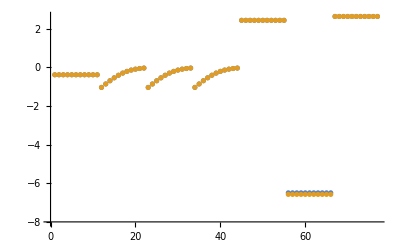

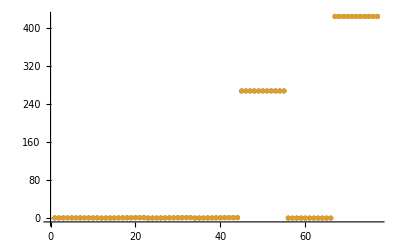

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

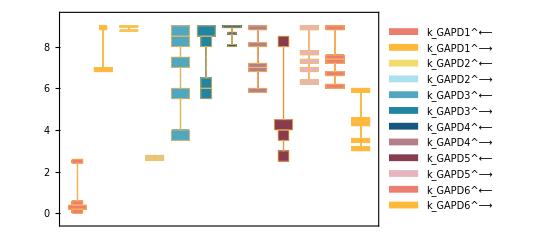

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

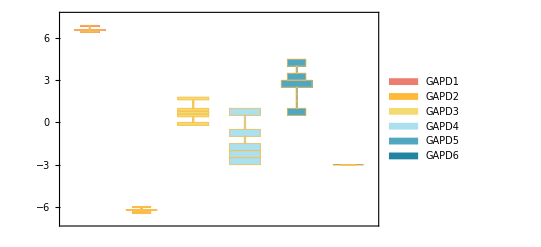

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

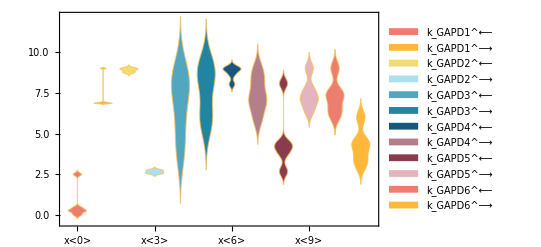

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

RegularExpression::msg22: Unmatched parentheses in RegularExpression[C:\MASSef\examples\fit_GAPD\input\(.*)\.txt]→$1.

General::stop: Further output of RegularExpression::msg22 will be suppressed during this calculation.

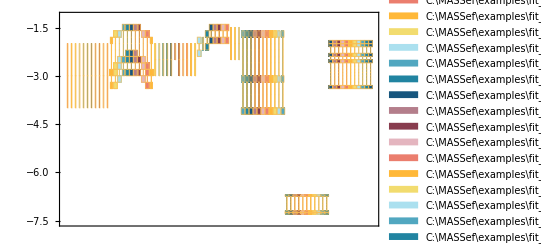

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000452265 | 0.503328
0.00089 | 0.000901619 | 1.30553
0.00053 | 0.000529605 | 0.0745818

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 4.00764×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 0.00011521

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408192 | 0.0470198